## Walker — PS 3 — 2025-01-24

## Section 9

```mathematica
Manipulate[Range[n],{n,0,100}]
Manipulate[ListPlot[Range[n]],{n,5,50}]
Manipulate[Column[Table[x,n]],{n,1,10}]
Manipulate[Graphics[Style[Disk[],Hue[n]]],{n,0,1}]
Manipulate[Graphics[Style[Disk[],RGBColor[red,green,blue]]],{red,0,1},{green,0,1},{blue,0,1}]
Manipulate[IntegerDigits[n],{n,1000,9999}]
Manipulate[Table[Hue[c],{c,0,1,1/n}],{n,5,50}]
Manipulate[Table[Graphics[Style[RegularPolygon[6],Hue[h]]],n],{n,1,10,1},{h,0,1}]
Manipulate[Graphics[Style[RegularPolygon[s],color]],{s,5,20,1},{color,{Red,Yellow,Blue}}]
Manipulate[PieChart[Table[1,n]],{n,1,10,1}]
Manipulate[BarChart[IntegerDigits[n]],{n,100,999,1}]
Manipulate[Table[RandomColor[],n],{n,1,50,1}]
Manipulate[Column[Table[b^e,{e,1,m,1}]],{b,1,25,1},{m,1,10,1}]
Manipulate[NumberLinePlot[Range[10]^n],{n,0,5,1}]
Manipulate[Graphics3D[Style[Sphere[],Hue[color]]],{color,0,1/3}]
```

## Section 10

```mathematica
ColorNegate[EdgeDetect[-Graphics-]]
Manipulate[Blur[-Graphics-,n],{n,0,20}]
Table[EdgeDetect[Blur[-Graphics-,n]],{n,0,20}]
ImageCollage[{-Graphics-,Blur[-Graphics-],EdgeDetect[-Graphics-],Binarize[-Graphics-]}]
ImageAdd[-Graphics-,Binarize[-Graphics-]]
Manipulate[EdgeDetect[Blur[-Graphics-,n]],{n,0,20}]
EdgeDetect[Graphics3D[Sphere[]]]
Manipulate[Blur[Graphics[Style[RegularPolygon[5],Purple]],n],{n,0,20}]
ImageCollage[Table[Graphics[Style[Disk[],RandomColor[]]],9]]
ImageCollage[Table[Graphics3D[Style[Sphere[],Hue[n]]],{n,0,1,0.2}]]
Table[Blur[Graphics[Disk[]],n],{n,0,30,5}]
ImageAdd[-Graphics-,Graphics[Disk[]]]
ImageAdd[-Graphics-,Graphics[Style[RegularPolygon[8],Red]]]
ImageAdd[-Graphics-,ColorNegate[EdgeDetect[-Graphics-]]]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

-Graphics-

-Graphics-

## Section 11

hellohello

ABCDEFGHIJKLMNOPQRSTUVWXYZ

zyxwvutsrqponmlkjihgfedcba

AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT

abcdef

t
th
thi
this
this 
this i
this is
this is 
this is a
this is ab
this is abo
this is abou
this is about
this is about 
this is about s
this is about st
this is about str
this is about stri
this is about strin
this is about string
this is about strings

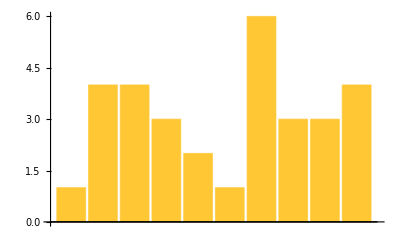

60266

9271

String or strings may refer to:

AMTTACCESEMTTTCTPP=ITTDBTTTT==DTLTTTSITIIDMTTAAATTTIASIBIAITITIITSI=CCAHTFTTTAEBNH=ITax()2{,THI=DHTTTTAB==CBTDETTITIRTZTT=PTEITDTTHACIINCTLOTIIIHBT==TTHTVTE=ECWATIHJTIIAATBAIL=TJFCJTHATHTTWITT=TTDTKIHKNNHPNIMTGFTTWISTITS=TTLTTTT=C=A=SH=TC==ATIET=WTTSC=TSC=TCATRDIRTPIWJSAIT=TES=TTSHTALTSG=AETTLSIETWOAMTTRACrRIIISFIIG=IDOHCIAMA=WTOBItSTBSIT=SMSTSS=SSCICW=T=TTMIAL=TITHTFMPWSTCBOTOI=ITTSTTITMWITC=PUTTS=MF=ATHHIT=PALTP=ETHOBSA=CTITTITCITA"=AWA=TMH=TQCVSLTTT=ACARPE=AT=====M

23

194

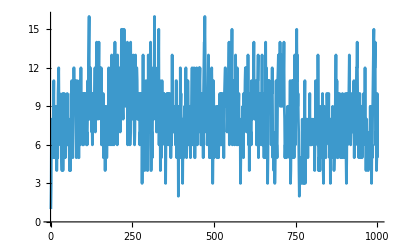

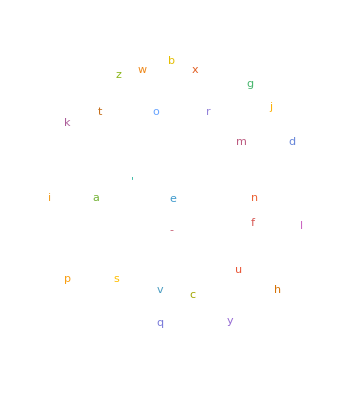

```mathematica
StringJoin["hello","hello"]
StringJoin[ToUpperCase[Alphabet[]]]
StringJoin[Reverse[Alphabet[]]]
StringJoin[Table["AGCT",100]]
StringTake[StringJoin[Alphabet[]],6]
Column[Table[StringTake["this is about strings",n],{n,1,21}]]
BarChart[StringLength[TextWords["A long time ago, in a galaxy far, far away"]]]
StringLength[WikipediaData["computer"]]
Length[TextWords[WikipediaData["computer"]]]
First[TextSentences[WikipediaData["strings"]]]
StringJoin[StringTake[TextSentences[WikipediaData["computers"]],1]]
Max[StringLength[WordList[]]]
Count[StringTake[WordList[],1],"q"]
ListLinePlot[StringLength[Take[WordList[],1000]]]
WordCloud[Characters[StringJoin[WordList[]]]]
```